```mathematica
ClearAll["Global`*"]
NX=300;timeby=0.;
gasesN={1,2,7,8,9,10,17,18,36,54,86};nn=3;
gases=ElementData[#]&/@gasesN;gas=gases⟦nn⟧;
gases⟦nn⟧=Framed[gases⟦nn⟧];gases
ρ0=ElementData[gas,"Density"]//QuantityMagnitude
k=ElementData[gas,"AdiabaticIndex"];
p0=Quantity[1, "Atmospheres"]//UnitConvert//QuantityMagnitude;e0=p0/(ρ0(k-1));
L=1;Kr=.5;j=0;
p=Table[0,NX];u=Table[0,NX];x=Table[0,NX+1];
e=Table[0,NX];ρ=Table[0,NX];umax={};ukin=Table[0,NX];
τ=0;t=Table[0,NX];h=Table[0,NX];f=Table[0,7,1];fcnt=0;
tg=Table[0,1];
step=10;ladd:={e,u,p,x,ρ,ukin};
add[x_]:=AppendTo[f⟦#⟧,x⟦#⟧]&/@Range[Length[ladd]];
la={"e","u","p","x","ρ","ukin"};
For[i=1,i≤ NX,i++,
ρ⟦i⟧=ρ0;e⟦i⟧=e0;p⟦i⟧=p0;u⟦i⟧=0.;
x⟦i⟧=L i/NX;x⟦i+1⟧=L( i+1)/NX;];
add[ladd];i=NX;p⟦i⟧=0;ρ⟦i⟧=0;
```

{hydrogen,helium,nitrogen,oxygen,fluorine,neon,chlorine,argon,krypton,xenon,radon}

1.251

```mathematica
timet=AbsoluteTime[];
While[True,j++;
For[i=1,i< NX,i++,h⟦i⟧=ρ⟦i⟧(x⟦i+1⟧-x⟦i⟧);
t⟦i⟧=Abs@((Kr h⟦i⟧)/(√(k p⟦i⟧ρ⟦i⟧)))];
τ=Min[t⟦;;NX-1⟧];(*If[p⟦1⟧≥.999p0,*)timeby+=τ;
For[i=2,i≤ NX,i++,
u⟦i⟧=u⟦i⟧-(τ (p⟦i⟧-p⟦i-1⟧))/(1/2 (ρ⟦i-1⟧ (x⟦i⟧-x⟦i-1⟧)+ρ⟦i⟧ (x⟦i+1⟧-x⟦i⟧)))];
For[i=1,i≤  NX,i++,x⟦i⟧=x⟦i⟧+u⟦i⟧ τ];
For[i=1,i< NX,i++,
ρt=1/(1/ρ⟦i⟧+τ/h⟦i⟧(u⟦i+1⟧-u⟦i⟧)); e⟦i⟧=(e⟦i⟧-p⟦i⟧(1/ρt-1/ρ⟦i⟧)/2)/(1+(ρt(k-1))/2(1/ρt-1/ρ⟦i⟧));
ρ⟦i⟧=ρt;p⟦i⟧=ρ⟦i⟧(k-1)e⟦i⟧;
ukin⟦i⟧=(u⟦i⟧u⟦i⟧)/2;];i=NX;
ρ⟦i⟧=0;p⟦i⟧=0;e⟦i⟧=e⟦i⟧;
If[Mod[j,step]==0,add[ladd];fcnt++;];
AppendTo[umax,Max[u]];
AppendTo[tg,timeby];
If[p⟦1⟧<p0*0.49999,add[ladd];fcnt++;Break[];];
];StringTemplate["Произведен расчет `2` ячеек  разностной сетки за `1` секунд"][AbsoluteTime[]-timet,j NX]
```

Произведен расчет 228000 ячеек  разностной сетки за 9.5755477 секунд

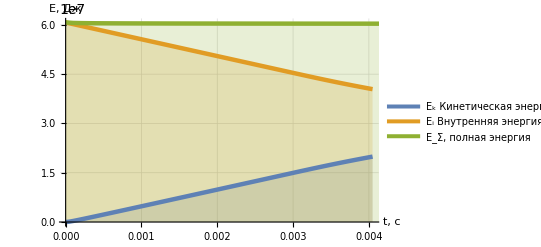

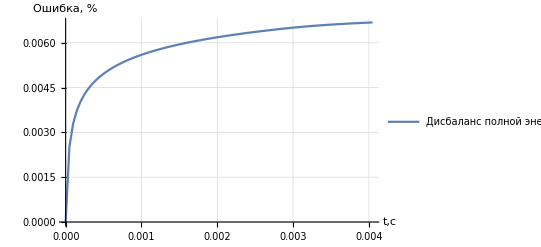

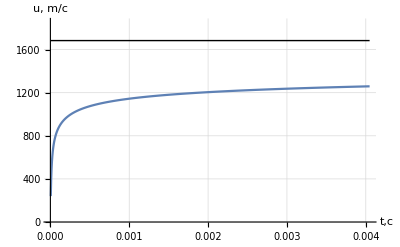

Предельная скорость истечения в пустоту 1683.69597442
Теоретическая скорость волны разрежения в среде: 336.73919488 м/с, из расчета: 247.00022906 м/с. 
Погрешность определения скорости 0.26649397 %

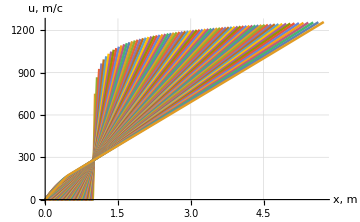

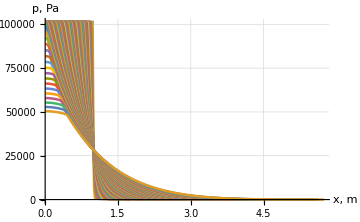

```mathematica
Subscript[E, p]=f⟦1⟧⟦2;;⟧;Subscript[E, k]=f⟦6⟧⟦2;;⟧;
Epls=Total[Subscript[E, p][[#]]]&/@Range[fcnt];Ekls=Total[Subscript[E, k][[#]]]&/@Range[fcnt];
tt=tg[[;;;;step]];
Eplst=Transpose[{tt,Epls}];Eklst=Transpose[{tt,Ekls}];
ListLinePlot[{Eklst,Eplst,Eklst+Eplst},PlotRange->{{0,Max[tt]},{All,All}},PlotLegends->{"E_k Кинетическая энергия","E_i Внутренняя энергия","E_Σ, полная энергия"},GridLines->Automatic,Filling->Bottom,PlotStyle->Thickness[.008],AxesLabel->{"t, c","E, Дж"}]

ListLinePlot[Transpose[{tt,Abs@((NX e0-(Ekls+Epls))/(NX e0))}],PlotRange->All,GridLines->Automatic,PlotLegends->{"Дисбаланс полной энергии"},AxesLabel->{"t,c","Ошибка, %"}]
umaxist=2/(k-1)√((k p0)/ρ0);
utg=Transpose[{tg[[2;;]],umax}];
ListLinePlot[utg,PlotRange->{{0,All},{0,umaxist+.1umaxist}},AxesLabel->{"t,c","u, m/c"},GridLines->Automatic,Epilog->Line[{{0,umaxist},{Max[tg],umaxist}}]]
a=f;Clear[u,p,x];u=a⟦2⟧;p=a⟦3⟧;x=a⟦4⟧;
u=u⟦2;;⟧;p=p⟦2;;⟧;x=x⟦2;;⟧;
x=x⟦#⟧⟦;;-2⟧&/@Range[fcnt];
err=N[Abs@((√(k p0/ρ0)-L/timeby)/(√(k p0/ρ0))),2];
StringTemplate["Предельная скорость истечения в пустоту `1`
Теоретическая скорость волны разрежения в среде: `3` м/с, из расчета: `4` м/с. 
Погрешность определения скорости `2` %"][umaxist,err,√(k p0/ρ0),L/timeby]
ux=Transpose[{x⟦#,All⟧,u⟦#,All⟧}]&/@Range[fcnt];
px=Transpose[{x⟦#,All⟧,p⟦#,All⟧}]&/@Range[fcnt];
ListLinePlot[ux,PlotRange->{{0,All},{0,All}},ImageSize->Medium,GridLines->Automatic,PlotLegends->"Распределение  массовой скорости",AxesLabel->{"x, m","u, m/c"},PlotStyle->Thickness[.005]]

ListLinePlot[px,PlotRange->{{0,All},{0,All}},ImageSize->Medium,GridLines->Automatic,PlotLegends->"Распределение  давления",AxesLabel->{"x, m","p, Pa"},PlotStyle->Thickness[.005]]
```

```mathematica
Export["C:\\Users\\Admin\\Desktop\\МСС курсач\\4.pdf",%3192,"PDF"]
```

C:\Users\Admin\Desktop\МСС курсач\4.pdf

```mathematica
Export["C:\\Users\\Admin\\Desktop\\МСС курсач\\4.pdf",%3129,"PDF"]
```

C:\Users\Admin\Desktop\МСС курсач\4.pdf

```mathematica
timeby
```

0.00288256

```mathematica
Max[tg]
```

0.00404177

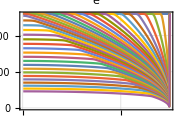
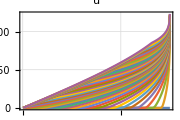
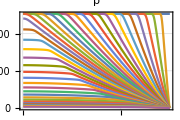
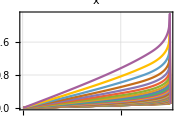
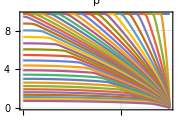
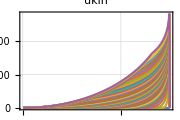

```mathematica
ListLinePlot[f⟦#⟧⟦2;;⟧,ImageSize->Small,PlotRange-> {{0,NX},{0,All}},Frame->True,GridLines->Automatic,PlotLabel->la⟦#⟧,AspectRatio->2/3]&/@Range[Length[ladd]]
```

1684.

1532.95

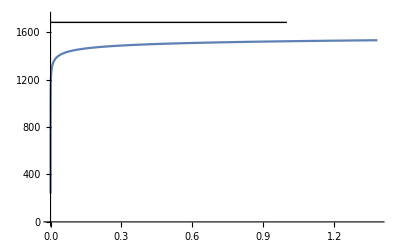

-0.0895354

```mathematica
mm=2/(k-1)√((k p0)/ρ0)
Max[umax]
ListLinePlot[utg,PlotRange->{{0,Max[tg]},{0,mm+50}},Epilog->Line[{{0,mm},{1,mm}}]]
(Max[umax]-mm)/mm
```